```mathematica
Subscript[g, N]=4 7/8;
Subscript[T, 0]=100;
Subscript[m, N]=100;
Subscript[g, 0]=2+4 7/8+2 3 7/8;
Subscript[M, pl]=1.22 10^22;
τ=10; (*sec*)
Γ=τ^-1 6.58 10^-22;
```

## Matter-radiation equality due to relativistically decoupled sterile neutrinos

Consider the system of radiation-dominated plasma with sterile neutrinos that decoupled at temperature T_0:
	ρ = ρ_0+ρ_N
	ρ_0=π^2/30 g_0 T^4
	ρ_N=π^2/30 g_N T^4 		at early times
	ρ_N=m_N n_N 		at small temperatures

Assuming that sterile neutrinos decoupled at the time t<τ=1/Γ, evolution of their energy density is governed by equation

	dρ_N/dt=-3 Hρ_N-Γρ_N 	(dn_N/dt=-3 Hn_N-Γn_N, ρ_N=m_N n_N)

At the moment of decoupling g_*=g_0+g_N and at the moment of matter-radiation equality g_*∼2 g_0

```mathematica
Manipulate[Module[{t,γ,δρ,Γ},(
Γ=τ^-1 6.58 10^-22;
t[T_,g_]:=0.301 g^(-1/2)Subscript[M, pl] T^-2;

γ=Subscript[g, 0]/Subscript[g, N];
δρ[T_]:=γ T/Subscript[T, 0]((2γ)/(1+γ))^(1/4)E^(Γ t[T,2 Subscript[g, 0]]);
roots=NSolve[{δρ[T]==1,T<Subscript[T, 0]},T]//Quiet;
LogLogPlot[{Evaluate[δρ[T]],1},{T,Subscript[T, 0],10^-2},
AxesLabel->{"T, MeV","ρ_rad/ρ_N"},
PlotLabel->"Matter domination at ρ_rad/ρ_N<1",
ImageSize->Large,
Epilog->Join[
{PointSize[.02]},Flatten[{Point[{Log[T],Log[1]}],Text[Style[T,FontSize->15],{Log[T],Log[0.6]}]}/.T-> First[#]&/@Values[roots]]]
]
)],{{Subscript[T, 0],100,"T_0, MeV"},0,10^4,Appearance->"Open"},{{τ,10,"τ, sec"},10^-2,10^4,Appearance->"Open"}]
```

## Matter-radiation equality due to non-relativistically decoupled sterile neutrinos (seems impossible)

Consider the system of radiation-dominated plasma with sterile neutrinos that decoupled at temperature T_0:
	ρ = ρ_0+ρ_N
	ρ_0=π^2/30 g_0 T^4
	ρ_N=m_N n_N 

At the moment of decoupling g_*∼g_0 and at the moment of matter-radiation equality g_*∼2 g_0

{}

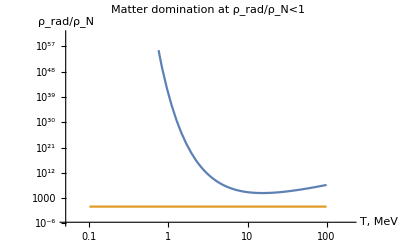

```mathematica
Module[{t,γ,δρ,n},(
t[T_,g_]:=0.301 g^(-1/2)Subscript[M, pl] T^-2;
Subscript[n, N][T_]:=(Subscript[m, N]/(2π T))^(3/2)E^(-Subscript[m, N]/T);

γ=Subscript[g, 0]/Subscript[g, N];
δρ[T_]:=γ (π^2/30 T^4)/(Subscript[m, N] Subscript[n, N][T])  T/Subscript[T, 0](2)^(1/4)E^(Γ t[T,2 Subscript[g, 0]]);

Print[NSolve[{
δρ[T]==1,
T<Subscript[T, 0]
},T]];
Print[LogLogPlot[{Evaluate[δρ[T]],1},{T,10^2,10^-1},AxesLabel->{"T, MeV","ρ_rad/ρ_N"},PlotLabel->"Matter domination at ρ_rad/ρ_N<1"]];
)]
```